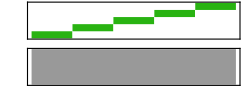

```mathematica
Sound[SoundNote[#,8,"Seashore"]&/@Range[0,4]]
```

```mathematica
Export["c:/chunqingbuluo/music/ListPlay_random_samplerate1024.wav",%]
```

c:/chunqingbuluo/music/ListPlay_random_samplerate1024.wav

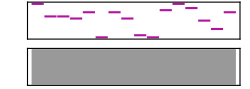

```mathematica
Sound[SoundNote[#,1,"Sweep"]&/@RandomInteger[16,16]]
```

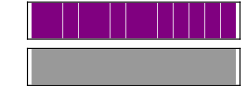

```mathematica
Sound[SoundNote["BellTree",#]&/@RandomInteger[2,16]]
```

```mathematica
Import[ "ExampleData/rule30.wav","Data" ]
```

{{0.,-0.0078125,-0.0078125,-0.015625,-0.015625,-0.0078125,-0.0078125,-0.0078125,-0.0078125,0.,0.,0.,0.,0.,«79352»,-0.0078125,-0.0078125,0.,0.,0.,0.,0.,-0.0078125,-0.0078125,-0.0078125,-0.0078125,-0.0078125,-0.0078125,-0.0078125}}

```mathematica
Sound[ListPlay[Random[190]]]
```

Random::randt: Type specification 190 in Random[190] should be Real, Integer, or Complex.

ListPlay::lsamps: The first argument to ListPlay must be a list of samples or a list of lists of samples.

```mathematica
ListPlay[RandomReal[1,{19000}],SampleRate->1000]
```

-Graphics-